# Image Processing with the Wolfram Language

## Giulio Alessandrini, WRI

## Outline

Basics

Creation and Import

Properties and Options

ImageType

Applications

Filtering

What is a filter?

Filtering: measure image properties

Filtering: applying artistic effects

Applications

Morphology

Structuring Elements

Basic Operations (Dilation & Erosion)

Advanced Operations (Opening, Closing, ...)

Application Examples

Segmentation

Thresholding

Clustering

Region Growing

Watersheds

Active contours

Grow-Cut

## Basics

### Creation and Import

### Properties and Options

### ImageType

### Applications

## Basics: Creation and Import

In the Wolfram Language, images and volumetric data are stored in Image and Image3D expressions.

Create 2D and 3D images from arrays of data:

```mathematica
Image[({{({{0}, {0.6}, {0}}), ({{0.4}, {0.1}, {0.8}}), ({{0.7}, {0.9}, {0.7}})}, {({{1}, {0}, {0.9}}), ({{0.6}, {0.6}, {1}}), ({{1}, {0.8}, {0.3}})}}),ColorSpace->"RGB", Interleaving->True]
```

```mathematica
Image[{({{0, 0.4, 0.7}, {1, 0.6, 1}}),({{0.6, 0.1, 0.9}, {0, 0.6, 0.8}}),({{0, 0.8, 0.7}, {0.9, 1, 0.3}})},ColorSpace->"RGB", Interleaving->False]
```

```mathematica
Image3D[{({{0, 0.4, 0.7}, {1, 0.6, 1}}),({{0.6, 0.1, 0.9}, {0, 0.6, 0.8}}),({{0, 0.8, 0.7}, {0.9, 1, 0.3}})}]
```

Extract samples from the built-in example data library:

```mathematica
vol=ExampleData[{"TestImage3D","CTengine"}]
```

or load image files, local or remote:

```mathematica
img=Import["https://www.wolfram.com/events/technology-conference-eu/2015/images/photo_0.jpg"]
```

## Basics: Properties and Options

### Pixel/Voxel Dimensions

Size given in width×height or width×depth×height:

```mathematica
ImageDimensions[img]
```

{500,234}

```mathematica
ImageDimensions[vol]
```

{256,256,110}

### Channels

Number of channels per pixel:

```mathematica
ImageChannels[img]
```

3

```mathematica
ImageChannels[vol]
```

1

### Color Space

Color space being used to interpret the image channels:

```mathematica
ImageColorSpace[img]
```

RGB

```mathematica
ImageColorSpace[vol]
```

Grayscale

Possible color spaces:

```mathematica
TableForm[
{{"\"Grayscale\"","gray level", "no"},{"\"RGB\"","red, green, blue", "no"},{"\"CMYK\"","cyan, magenta, yellow, black", "no"},{"\"HSB\"","Cell["hue, saturation, brightness", "TableText"]", "no"},{"\"XYZ\"","CIE XYZ", "yes"},{"\"LAB\"","CIE L","yes"},{"\"LCH\"","CIE L^*C^*h(a^*b^*)","yes"},{"\"LUV\"","CIE L","yes"},{Automatic,"no color space specified","no"}},
TableHeadings-> {None,{"Colorspace","description","device-independent"}}]
```

Colorspace | description | device-independent
"Grayscale" | gray level | no
"RGB" | red, green, blue | no
"CMYK" | cyan, magenta, yellow, black | no
"HSB" | Cell["hue, saturation, brightness", "TableText"] | no
"XYZ" | CIE XYZ | yes
"LAB" | CIE L | yes
"LCH" | CIE L^*C^*h(a^*b^*) | yes
"LUV" | CIE L | yes
Automatic | no color space specified | no

Color profile for the exact device-independent mapping of channel values into colors:

```mathematica
Options[img,ColorSpace]
```

### Meta Information

Extracting meta-information from an imported image:

```mathematica
img=-Graphics-;
```

```mathematica
Options[img,MetaInformation]
```

Extracting a specific meta-information:

```mathematica
exif=Dataset[Lookup[Options[img,MetaInformation][[1,2]],"Exif"]]
```

```mathematica
exif["DateTime"]
```

## Basics: ImageType

This imports a color image.

```mathematica
img=Import["ExampleData/lena.tif"]
```

Images are typically encoded by one Byte per pixel and channel:

```mathematica
ImageType[img]
```

Possible data types:

```mathematica
TableForm[
{{"\"Bit\"","integer 0 or 1", "yes", "yes"},{"\"Byte\"","integer 0 through 255", "yes", "yes"},{"\"Bit16\"","integer 0 through 65535", "yes", "yes"},{"\"Real32\"","single-precision real (32 bit)", "no", "no"},{"\"Real\"","double-precision real (64 bit)", "no", "no"}},
TableHeadings-> {None,{"data type","value range","clipping","quantization"}}]
```

data type | value range | clipping | quantization
"Bit" | integer 0 or 1 | yes | yes
"Byte" | integer 0 through 255 | yes | yes
"Bit16" | integer 0 through 65535 | yes | yes
"Real32" | single-precision real (32 bit) | no | no
"Real" | double-precision real (64 bit) | no | no

Bit, Byte or Bit16 encoding can only handle luminosity values between 0 and 1. Arithmetic results exceeding the [0,1] interval are clipped.
Thus, addition cannot be undone, if clipping occurred.

```mathematica
ImageSubtract[ImageAdd[img,0.5],0.5]
```

This does not happen for images with Real32 or Real64 floating point encoding:

```mathematica
ImageSubtract[ImageAdd[Image[img,"Real32"],0.5],0.5]
```

## Basics: Applications

### Steganography

```mathematica
image=ExampleData[{"TestImage","Lena"}]
```

```mathematica
dims=ImageDimensions[image]
```

```mathematica
channels=ImageChannels[image]
```

```mathematica
n=Times@@dims channels
```

```mathematica
imagedata=Flatten[ImageData[image,"Byte"]];
```

```mathematica
imagedata[[;;10]]
```

```mathematica
string="This is a very very secret message";
```

#### Encoding

```mathematica
message=(IntegerDigits[#,2,8]&)@*ToCharacterCode/@Characters[string]//Flatten
```

```mathematica
step=Floor[n/Length[message]]
```

```mathematica
imagedata[[;;step Length[message];;step]]
```

```mathematica
binarypixels=IntegerDigits[imagedata[[;;step Length[message];;step]],2,8];
Short[binarypixels]
```

```mathematica
binarypixels[[All,-1]]=message;
```

```mathematica
imagedata[[;;step Length[message];;step]]=FromDigits[#,2]&/@binarypixels;
```

```mathematica
newimage=Image[ArrayReshape[imagedata,Append[dims,channels]],"Byte"]
```

```mathematica
ImageDifference[image,newimage]
```

```mathematica
ImageAdjust[%]
```

#### Decoding

```mathematica
ClearAll[ExtractMessage]
ExtractMessage[image_Image,messageLength_Integer?Positive]:=
With[{step=Floor[Times@@ImageDimensions[image]ImageChannels[image]/(8messageLength)]},
StringJoin@*Map[(FromDigits[#,2]&)/*FromCharacterCode]@Partition[IntegerDigits[Flatten[ImageData[image,"Byte"]][[;;;;step]],2,8][[All,-1]],8]
]
```

```mathematica
ExtractMessage[image,StringLength[string]]
```

```mathematica
ExtractMessage[newimage,StringLength[string]]
```

#### Package it all in a function

```mathematica
ClearAll[EncodeMessage]
EncodeMessage::smallimg="The image provided is too small to contain the message. At least `1` pixels are needed.";
EncodeMessage[message_String,image_Image]:=
Module[
{
binarymessage,binarypixels,imagedata,
n=Times@@ImageDimensions[image]ImageChannels[image],
step
},

binarymessage=(IntegerDigits[#,2,8]&)@*ToCharacterCode/@Characters[message]//Flatten;
If[Length[binarymessage]>n,
Message[EncodeMessage::smallimg,Length[binarymessage]];
Return[$Failed]];

imagedata=Flatten[ImageData[image,"Byte"]];

step=Floor[n/Length[binarymessage]];
binarypixels=IntegerDigits[imagedata[[;;step Length[binarymessage];;step]],2,8];
binarypixels[[All,-1]]=binarymessage;

imagedata[[;;step Length[binarymessage];;step]]=FromDigits[#,2]&/@binarypixels;
Image[ArrayReshape[imagedata,Append[ImageDimensions[image],ImageChannels[image]]],"Byte"]
]
```

```mathematica
message=ExampleData[{"Text","DeclarationOfIndependence"}];
```

```mathematica
encodedimage=EncodeMessage[message,image]
```

```mathematica
ExtractMessage[encodedimage,StringLength[message]]
```

## Filtering

### What is a filter?

### Filtering: measure image properties

### Filtering: applying artistic effects

### Applications

## What is a filter?

A filter is a function applied to an image that returns another image

```mathematica
image↦f[image]
```

Many filters are built-in Wolfram Language functions

```mathematica
?*Filter
```

```mathematica
ArrayPlot[ArrayPad[GaussianMatrix[10],{{2,5},{2,5}},0],Mesh->All]
```

```mathematica
{image,ImageConvolve[image,GaussianMatrix[10]]}
```

## Filtering: extract image features

Filter can be used to identify specific features in images

### Edges

Convolve with the derivative of a Gaussian matrix to find the edges

```mathematica
Dx=ImageConvolve[image,GaussianMatrix[4,{1,0}]];
%//ImageAdjust
```

```mathematica
Dy=ImageConvolve[image,GaussianMatrix[4,{0,1}]];
%//ImageAdjust
```

```mathematica
ImageApply[Sqrt[#1^2+#2^2]&,{Dx,Dy}]//ImageAdjust
```

The built-in GradientFilter computes the gradient of the image intensity

```mathematica
GradientFilter[image,4]
```

Use ColorSeparate and ColorCombine to apply the gradient filter to each channel

```mathematica
ColorSeparate[image]
```

```mathematica
GradientFilter[#,4]&/@%
```

```mathematica
ColorCombine[%]//ImageAdjust
```

### Ridges

Write a custom filter using a mix of differential operators in order to detect ridges

```mathematica
img=-Graphics-;
```

```mathematica
ridgeFilter[img_,σ_:1] := Module[
{data = ImageData[img],Lxx,Lxy,Lyy},
{Lxx,Lxy,Lyy}=DerivativeFilter[data,{{0,2},{1,1},{2,0}},σ];
Image[
Chop[σ^(3/2)/2(√((Lxx - Lyy)^2+ 4 Lxy^2)-Lxx-Lyy)]
]
]
```

```mathematica
ridgeFilter[img,5]//ImageAdjust
```

Compare with the built-in RidgeFilter

```mathematica
RidgeFilter[img,5]//ImageAdjust
```

## Filtering: applying artistic effects

Filter can be also used to apply artistic effects to images

```mathematica
bird=-Graphics-
```

```mathematica
MinFilter[bird,5]
```

```mathematica
MaxFilter[bird,5]
```

```mathematica
ImageFilter[Max,bird,4]
```

```mathematica
ImageFilter[RandomChoice[Flatten[#,1]]&,bird,5]
```

## Applications: Inpaint

Total variation with a masking function m(x).

ArgMin[λ  Norm[u]_TV+∫_Ω (1-m(x)) (f(x)-u(x))^2 ⅆx,x∈BV(Ω)]

```mathematica
lincoln=-Graphics-;
```

```mathematica
Binarize@Dilation[Closing[-Graphics-,5],1]
```

```mathematica
Inpaint[lincoln, %,Method->"TotalVariation"]
```

## Applications: ImageDeconvolution

Total variation with respect to a functional that compares f(x) with K(x)⋆u(x) instead of u(x).
K(x) is the point spread function of the blur.

ArgMin[λ  Norm[u]_TV+∫_Ω (f(x)-K(x)⋆u(x))^2 ⅆx,x∈BV(Ω)]

### Black and white images

Test image :

```mathematica
snellenChart = ImagePad[-Graphics-,16,White];
```

Convolution kernel K:

```mathematica
K= GaussianMatrix[{16,8}];
MatrixPlot[K]
```

Blurred test image:

```mathematica
blurredChart=ImageConvolve[snellenChart,K]
```

Deconvolution I:

```mathematica
ImageDeconvolve[ blurredChart, GaussianMatrix[{16,8}],  Method->{"TotalVariation", "Regularization"-> 0},Padding-> White]
```

Deconvolution II: (more realistic)

```mathematica
ImageDeconvolve[ Image[blurredChart,"Byte"], GaussianMatrix[{16,8}],  Method->{"TotalVariation", "Regularization"-> 0.002},Padding-> White]
```

### Color images

```mathematica
lena=ExampleData[{"TestImage","Lena"}];
```

```mathematica
ImageConvolve[ImagePad[lena,20,Padding->Black],GaussianMatrix[20]]
```

```mathematica
ImageDeconvolve[%, GaussianMatrix[20],Padding->Black]
```

Remember to provide enough padding

```mathematica
ImageDeconvolve[ImageConvolve[lena,GaussianMatrix[20]], GaussianMatrix[20]]
```

## Morphology

Mathematical morphology includes theories and techniques for analyzing shapes and forms of the objects with applications in different areas of image processing and analysis including image filtering, segmentation, measurements and more.

### Structuring Elements

### Basic Operations (Dilation & Erosion)

### Advanced Operations (Opening, Closing, ...)

### Application Examples

## Morphology: Structuring Element (SE)

### Very commonly used structuring elements

Square or diamond shaped connectivity that includes the 4- or 8-connected neighbors around each image pixel. 
In Mathematica, these settings can be specified either explicitly using a matrix of 0s and 1s or via the CornerNeighbors option.

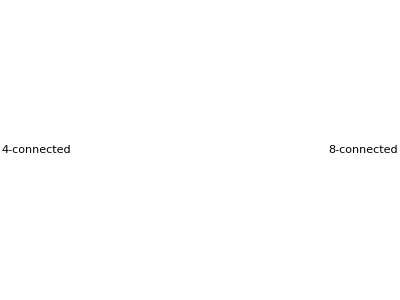

```mathematica
GraphicsRow[MapThread[Labeled[ArrayPlot[#[1,{5,5}],Mesh->All,ColorRules->{1->White,0->Black}],#2,ImageSize->150]&,{{CrossMatrix,BoxMatrix},Style[#,16]&/@{"4-connected","8-connected"}}]]
```

```mathematica
DynamicModule[
{img=-Graphics-},
Manipulate[
ColorCombine[{img,Dilation[img,ker[radius]],img}],
{{ker,CrossMatrix},{CrossMatrix->"Cross",BoxMatrix->"Box"}},{{radius,5},0,16}
]
]
```

### Arbitrary structuring elements

Other arbitrary shapes can also be used as structuring elements. Typically center of the SE is also included in the structure (with a value of 1), however, that is not a necessity.

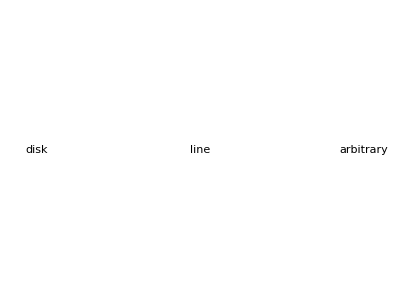

```mathematica
GraphicsRow[MapThread[Labeled[ArrayPlot[#,Mesh->All,ColorRules->{1->White,0->Black}],#2,ImageSize->100]&,{{DiskMatrix[5,{13,13}],ArrayPad[Dilation[IdentityMatrix[11],CrossMatrix[1]],1],ImageData[-Graphics-,"Bit"]},Style[#,16]&/@{"disk","line","arbitrary"}}]]
```

## Morphology: Basic Operations (Dilation & Erosion)

Given binary images and their set descriptions, Dilation of set A by structuring element B is defined as the union (logical Or) of all translates A_b of A, the translates determined by the positions of the one-valued pixels of the structuring element B. Erosion is defined as the  intersection (logical And) of all translates A_-b of A.

Dilation:   δ_B(A)=A ⊕ B = ∪
b∈B A_b		Erosion:   ε_B(A)=A ⊖ B = ∩
b∈B A_-b

### Set operations to perform dilation with

```mathematica
kernel=-Graphics-;
```

### Binary dilation & erosion as filtering operations

```mathematica
With[{im1 =-Graphics-,dims=ImageDimensions[-Graphics-],ker=BoxMatrix[1]},
Manipulate[Module[{mask,tmp,im2},
im2=ImageAdd[im1,ImageMultiply[Image[ImageDifference[im1,Dilation[im1,ker]],"Byte"],.8]];
mask=Image[ArrayReshape[ConstantArray[1,loc],Reverse@dims],ImageSize->300];
tmp=ImageAdd[ImageMultiply[im2,mask],ImageMultiply[im1,ColorNegate[mask]]];
Image[HighlightImage[tmp,ImageReflect@ImageCompose[ConstantImage[0,dims],ImageReflect@Image[ker+.2],{Mod[loc-1,dims[[1]]],Quotient[loc-1, dims[[1]]]}],"HighlightColor"->Cyan],ImageSize->300]],{loc,1,Times@@dims,1}]]
```

```mathematica
With[{im1 =-Graphics-,dims=ImageDimensions[-Graphics-],ker=BoxMatrix[1]},
Manipulate[Module[{mask,tmp,im2},
im2=ImageSubtract[im1,ImageMultiply[Image[ImageDifference[im1,Erosion[im1,ker]],"Byte"],.8]];
mask=Image[ArrayReshape[ConstantArray[1,loc],Reverse@dims],ImageSize->300];
tmp=ImageAdd[ImageMultiply[im2,mask],ImageMultiply[im1,ColorNegate[mask]]];
Image[HighlightImage[tmp,ImageReflect@ImageCompose[ConstantImage[0,dims],ImageReflect@Image[ker+.2],{Mod[loc-1,dims[[1]]],Quotient[loc-1, dims[[1]]]}],"HighlightColor"->Cyan],ImageSize->300]],{loc,1,Times@@dims,1}]]
```

Dilation & erosion with different SEs of the binary image

```mathematica
With[
{i=-Graphics-,
selist={DiskMatrix[5],IdentityMatrix[11],BoxMatrix[{0,5},{11,11}]}},
{ArrayPlot[#,Mesh->All,ColorRules->{0->Black,1->White},ImageSize->100]&/@selist,
Dilation[i,#]&/@selist,
Erosion[i,#]&/@selist
}//Grid
]
```

-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-

#### Grayscale dilation & erosion

```mathematica
With[{im1 =-Graphics-,ker=BoxMatrix[1]},
Manipulate[Module[{mask,tmp,im2,dims},
dims=ImageDimensions[im1];
im2=Dilation[im1,ker];
mask=Image[ArrayReshape[ConstantArray[1,loc],Reverse@dims],ImageSize->200];
tmp=ImageAdd[ImageMultiply[im2,mask],ImageMultiply[im1,ColorNegate[mask]]];
Image[HighlightImage[tmp,ImageReflect@ImageCompose[ConstantImage[0,dims],ImageReflect@Image[ker+.2],{Mod[loc-1,dims[[1]]],Quotient[loc-1, dims[[1]]]}],"HighlightColor"->Cyan],ImageSize->200]],{loc,1,Times@@ImageDimensions[im1],1}]]
```

```mathematica
With[{im1 =-Graphics-,ker=BoxMatrix[1]},
Manipulate[Module[{mask,tmp,im2,dims},
dims=ImageDimensions[im1];
im2=Erosion[im1,ker];
mask=Image[ArrayReshape[ConstantArray[1,loc],Reverse@dims],ImageSize->200];
tmp=ImageAdd[ImageMultiply[im2,mask],ImageMultiply[im1,ColorNegate[mask]]];
Image[HighlightImage[tmp,ImageReflect@ImageCompose[ConstantImage[0,dims],ImageReflect@Image[ker+.2],{Mod[loc-1,dims[[1]]],Quotient[loc-1, dims[[1]]]}],"HighlightColor"->Cyan],ImageSize->200]],{loc,1,Times@@ImageDimensions[im1],1}]]
```

Examples with different structuring elements

```mathematica
With[
{i=Image[ExampleData[{"TestImage", "Clock"}],ImageSize->All],
selist={DiskMatrix[10],IdentityMatrix[21],BoxMatrix[{0,10},{21,21}]}},
{ArrayPlot[#,Mesh->All,ColorRules->{0->Black,1->White},ImageSize->100]&/@selist,
Dilation[i,#]&/@selist,
Erosion[i,#]&/@selist
}//Grid
]
```

## Morphology: Advanced Operations

Many advanced operations can be derived from combining basic morphological operations: erosion and dilation. These operations have many applications in image restoration and cleaning as well as feature extraction and shape analysis through boundaries and skeletons.

### Opening & Closing

Opening:    γ_B(A)=δ_(B̃)(ε_B(A))		Closing:   ϕ_B(A)=ε_(B̃)(δ_B(A))

```mathematica
i=-Graphics-;
```

```mathematica
Closing[i,4]
```

```mathematica
Manipulate[Closing[i,r],{r,1,5}]
```

```mathematica
i=-Graphics-
```

```mathematica
Opening[i,DiskMatrix[3]]
```

### Top- hat transformations

top-hat:    THT_B(A)=I-γ_B(A)		bottom-hat:   BHT_B(A)=ϕ_B(A)-I

```mathematica
i=-Graphics-;
```

```mathematica
TopHatTransform[i,DiskMatrix[7]]
```

### Morphological Gradients

Beucher gradient:   ρ_B=δ_B-ε_B	Half gradients:   δ_B-I   or I-ε_B

```mathematica
i=-Graphics-;
```

```mathematica
ImageSubtract[Dilation[i,1],Erosion[i,1]]
```

#### Grayscale images

```mathematica
i=ExampleData[{"TestImage","Clock"}]
```

```mathematica
TabView[(ToString[#]->ImageSubtract[Dilation[i,#[3]],Erosion[i,#[3]]])&/@{CrossMatrix,DiskMatrix,BoxMatrix}]
```

### Hit-or-Miss transform

```mathematica
HitMissTransform[-Graphics-,{{-1},{1}}]
```

### Geodesic reconstruction

```mathematica
i=-Graphics-;marker=-Graphics-;
```

```mathematica
Manipulate[Dilation[marker,n],{n,1,30,5}]
```

```mathematica
Manipulate[GeodesicDilation[marker,i,n],{n,1,55,1}]
```

```mathematica
GeodesicDilation[marker,i]
```

### Filling transformation

```mathematica
FillingTransform[-Graphics-]
```

```mathematica
FillingTransform[-Graphics-,-Graphics-]
```

### Distance Transformation

Distance transformation can be computed as a series of erosion operations.

```mathematica
With[{i=-Graphics-},Manipulate[Erosion[i,r],{r,1,70}]]
```

```mathematica
DistanceTransform[-Graphics-]//ImageAdjust
```

### Skeletonization

Thinning operation and converting to a graph representation of the skeleton

```mathematica
Thinning[-Graphics-,Infinity,0.9]
```

```mathematica
MorphologicalGraph[%]
```

Skeleton transformation and processing for reshaping

```mathematica
(skel=SkeletonTransform[-Graphics-])//ImageAdjust
```

```mathematica
(skel2=Pruning[skel,30])//ImageAdjust
```

```mathematica
InverseDistanceTransform[skel2]
```

## Morphology: Application Examples

### Correction for uneven illumination

```mathematica
TopHatTransform[-Graphics-,2]
```

### Noise removal

```mathematica
img=i=-Graphics-
```

```mathematica
Inpaint[img, ImageAdd[MaxDetect[img],MinDetect[img]],Method->"Diffusion"]
```

### Connected components

```mathematica
MorphologicalComponents[-Graphics-]//Colorize
```

### Hole filling

```mathematica
FillingTransform[-Graphics-]
```

### Component cleaning

```mathematica
DeleteBorderComponents[-Graphics-]
```

```mathematica
DeleteSmallComponents[%,20]
```

### Separation of overlapping components

```mathematica
WatershedComponents[GradientFilter[-Graphics-,1],-Graphics-,Method->"Rainfall"]//Colorize
```

## Segmentation

### Thresholding

### Clustering

### Region Growing

### Watersheds

### Active contours

### Grow-Cut

## Segmentation: Thresholding

### Simple thresholding

The simplest segmentation technique is thresholding. Pixels with values above a certain constant are selected:

```mathematica
image=-Graphics-
```

```mathematica
Binarize[image]
```

### Adaptive thresholding

A locally adaptive thresholding is more robust :

```mathematica
LocalAdaptiveBinarize[image,40,{.8,.1}]
```

```mathematica
TextRecognize[%]
```

### Hysteresis thresholding

Combine two binary images computed with two levels of thresholding to perform reconstruction by dilation. Binary image with a higher threshold is used to specify marker points and the binary image with the lower threshold is used to define all connected regions to those important marker points.

```mathematica
g=GradientFilter[-Graphics-,2]//ImageAdjust
```

```mathematica
{b1,b2}=Binarize[g,#]&/@{.3,.6}
```

```mathematica
GeodesicDilation[b2,b1]
```

This operation is already built-in as MorphologicalBinarize:

```mathematica
MorphologicalBinarize[g,{.3,.6}]
```

## Segmentation: Clustering

Clustering of grayscale or color pixel values is another way of segmenting an image into multiple components.
Note, that the spatial relations of pixels are not taken into account and that the pixels are clustered only based on their color values. 
For the following satellite photography (source link) we utilize K-means, one of the best known clustering techniques for image segmentation.

```mathematica
satimg=-Graphics-;
```

```mathematica
ClusteringComponents[ColorConvert[satimg,"LAB"],4, Method-> "KMeans"]//Colorize
```

To achieve a better spatial coherence of the segmentation, one should regularize the image beforehand. 
The MeanShiftFilter returns the mean pixel value of a neighborhood, but taking into account
only those pixels whose value is within a Euclidean distance d from the center pixel.

```mathematica
ClusteringComponents[
MeanShiftFilter[ColorConvert[satimg,"LAB"],2,1/6],
4,
Method-> "KMeans"
]//Colorize
```

## Segmentation: Region Growing

Grow a segment starting with a seed:

```mathematica
img=-Graphics-;seed=-Graphics-;
```

The seed grows as long as the values of neighboring pixels do not exceed the given threshold:

```mathematica
seg=FillingTransform@RegionBinarize[img,seed,0.085]
```

Display the resulting segmentation on the original image:

```mathematica
HighlightImage[img,seg]
```

## Segmentation: Watersheds

Heart chamber segmentation:

```mathematica
img=-Graphics-;
```

Use local maxima of smoothed data as markers:

```mathematica
markers=MaxDetect[GaussianFilter[img,25],Padding->1];
HighlightImage[img,markers,Method->{"DiskMarkers",5}]
```

The watershed segmentation seeks the water basins in the given "gradient" mountain range:

```mathematica
ListPlot3D[ImageData[GradientFilter[img,3],DataReversed-> True], PlotRange-> All, BoxRatios-> {1,1,1/10}, Boxed-> False, Mesh-> False,ColorFunction-> "AlpineColors", Axes-> None]
```

Watershed segmentation using detected marker points:

```mathematica
WatershedComponents[GradientFilter[img,3],markers]//Colorize
```

### Fun Example

Solve a maze puzzle using watershed transform:

```mathematica
maze=-Graphics-;
```

The water ridge is the path through the maze:

```mathematica
path=ColorNegate[Image[WatershedComponents[maze],"Bit"]];
HighlightImage[maze,path]
```

## Segmentation: Active contours (Chan-Vese)

The Chan–Vese segmentation of an image domain Ω into the two segments 𝒟 and Ω\𝒟 with contour Γ==∂𝒟 minimizes the following functional F of image f:

-Graphics-

Specify both foreground and background colors for creating an initial marker:

```mathematica
ChanVeseBinarize[-Graphics-,{{Red,Blue}}]
```

Decrease the penalty for the contour Γ==∂𝒟 to improve the segmentation of a satellite image:

```mathematica
Manipulate[ChanVeseBinarize[-Graphics-,Automatic,{μ}],{{μ,.2},0,2}]
```

## Segmentation: Grow-Cut

An interactive Grow-Cut example:

Select the fore- and background interactively with the mouse and let the grow-cut algorithm do the rest:

```mathematica
DynamicModule[
{pen,erasor,segmentation,mask, color, img=-Graphics-},
pen = SetAlphaChannel[#,#]&@Image[DiskMatrix[4],"Bit"];
erasor=ColorNegate[pen];
segmentation = ConstantImage[1,ImageDimensions[img]];
mask = Table[ConstantImage[0,ImageDimensions[img],"Bit"],{3}];
Deploy@Panel[Grid[{
{SetterBar[Dynamic[color],{1-> "Background",2-> "Foreground"}],
Button["Clear",mask = Table[ConstantImage[0,ImageDimensions[img],"Bit"],{3}];segmentation = ConstantImage[255,ImageDimensions[img],"Byte"]],Button["Grow Cut", If[Not[And@@Map[(ImageMeasurements[#,"Max"]==0)&,mask]],segmentation =Image[GrowCutComponents[img,mask, MaxIterations-> 256]-0.7];
mask = Table[ConstantImage[0,ImageDimensions[img],"Bit"],{3}]]]},
{EventHandler[
Dynamic@Deploy@Image[ImageCompose[SetAlphaChannel[img,segmentation],SetAlphaChannel[ColorCombine[mask],ImageAdd@@mask]],ImageSize->ImageDimensions[img]],
{"MouseDragged":>If[
CurrentValue["ShiftKey"],
mask⟦color⟧ = ImageCompose[mask⟦color⟧,erasor,MousePosition["EventHandlerAbsolute"]/CurrentValue[Magnification]],
mask⟦color⟧ = ImageCompose[mask⟦color⟧,pen,MousePosition["EventHandlerAbsolute"]/CurrentValue[Magnification]]
]}
],
SpanFromLeft}}
]]
]
```

# The End